```mathematica
(* Available Plays *)
plays={"Midsummer Night's Dream", "Romeo and Juliet","Hamlet","King Lear", "Antigone"};
```

```mathematica
(* Process Plays *)
(*sceneNumbers={"1.1","1.2","2.1","2.2","3.1","3.2","4.1","4.2","5.1"};*)

SetDirectory[NotebookDirectory[]];
files=FileNames["*.txt",NotebookDirectory[]];
text=StringJoin[Import[#]&/@files⟦22;;47⟧];
speakerOrder=StringCases[text,Shortest["<b>"~~x__~~"</b>"]->x]//Flatten;
nameList=speakerOrder//DeleteDuplicates;
```

```mathematica
(* Separates lines of text ready for sentiment analysis *)
lines=StringSplit[text,Shortest["<b>"~~x__~~"</b>"]];
lines=StringDelete[lines,Shortest["<i>"~~x__~~"</i>"]];
lines=StringDelete[lines,Shortest["["~~x__~~"]"]];
lines=StringDelete[lines,Shortest["<"~~x___~~">"]]//Rest;
lines=StringDelete[lines,Shortest["Shakespeare homepage"~~x__~~"Enter"]];
sentences=lines//TextSentences;
lineLength=Length/@sentences;
```

```mathematica
(* Create directed edges for graph *)
speakerBySentence=Table[Table[speakerOrder⟦i⟧,Length[sentences⟦i⟧]],{i,1,Length[lines]}]//Flatten;
recipientByLine=Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}];
recipientByLine=Prepend[recipientByLine,Table[speakerOrder⟦2⟧,Length[First[sentences]]]];
recipientBySentence=Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}]//Flatten;
recipientBySentence=Nest[Prepend[speakerOrder⟦2⟧],recipientBySentence,Length[First[sentences]]];

emphasis=WordFrequency[Flatten[sentences],#,IgnoreCase->True]&/@nameList;
diffRecipientPos=Position[emphasis,_?Positive];
diffRecipientPos=SortBy[diffRecipientPos,Last];
diffRecipient=First/@diffRecipientPos;
diffSentence=Last/@diffRecipientPos;

brokenInd=TakeList[Range[Length[recipientBySentence]],lineLength];
sentenceToLineRules=Table[i->First@@Position[brokenInd,i],{i,1,Length[recipientBySentence]}];
lineIndOfSentences=Range[Length[recipientBySentence]]/.sentenceToLineRules;
sentenceNumOfDiffLine[x_]:=Last@diffRecipientPos⟦x⟧-Total[lineLength⟦;;lineIndOfSentences⟦Last@diffRecipientPos⟦x⟧⟧-1⟧];

For[i=1,i≤Length[diffRecipientPos],i++,
recipientByLine⟦lineIndOfSentences⟦Last@diffRecipientPos⟦i⟧⟧,sentenceNumOfDiffLine[i];;⟧=nameList⟦First@diffRecipientPos⟦i⟧⟧]

recipientBySentence=recipientByLine//Flatten;
finalRules=Table[speakerBySentence⟦i⟧->recipientBySentence⟦i⟧,{i,1,Length[speakerBySentence]}];
rules=DeleteCases[DeleteDuplicates[finalRules],x_->x_];
```

```mathematica
(* Implement Sentiment Analysis of lines *)
feelings=Classify["Sentiment",#,"Probabilities"]&/@sentences//Flatten;
```

```mathematica
(* Put sentiment into edges *)
{pos,neu,neg}=Table[feelings⟦i⟧[#],{i,1,Length[feelings]}]&/@{"Positive","Neutral","Negative"};
Health=(pos-neg)/(1+neu);
sentenceHealth={finalRules⟦#⟧,Health⟦#⟧}&/@Range[Length[Health]];
sentenceHealthFormat=Cases[sentenceHealth,{#,_}]&/@rules;
relationshipHealth=Table[Mean[Table[sentenceHealthFormat⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sentenceHealthFormat⟦i⟧]}]],{i,1,Length[sentenceHealthFormat]}];
```

```mathematica
(* Incorporate Frequency for into Health *)
freq=Table[Length[sentenceHealthFormat⟦i⟧],{i,1,Length[sentenceHealthFormat]}];
freqMultiplier[x_]:=(Log[x]+2)/2;
thickness=N[freq]/Max[N[freq]]*.012;
edgeWidth=Table[rules⟦i⟧->freqMultiplier[N[freq⟦i⟧]],{i,Length[rules]}];
```

```mathematica
(* Exclude Neutral/Conflicted Relationships *)
relationshipHealthFinal=relationshipHealth*N[freqMultiplier[freq]];
viableEdges=Position[relationshipHealthFinal,x_/;x>.30||x<-.30]//Flatten;
relationshipHealthFinalExc=Table[relationshipHealthFinal⟦i⟧,{i,viableEdges}];
viableFreq=Table[freq⟦i⟧,{i,viableEdges}];
viableThickness=Table[thickness⟦i⟧,{i,viableEdges}];
viableEdgeWidth=Table[edgeWidth⟦i⟧,{i,viableEdges}];
```

```mathematica
(* Modify the Graph with color (health) and width (frequency) *)
relationshipColors=Table[Blend[{Red,Green},(i+1)/2],{i,relationshipHealthFinalExc}]
```

{RGBColor[0.16013015602976677, 0.8398698439702332, 0.],RGBColor[0.06790749452383871, 0.9320925054761613, 0.],RGBColor[0.2863206854309388, 0.7136793145690612, 0.],RGBColor[0.27619545241760135, 0.7238045475823986, 0.],RGBColor[0.06268793308784848, 0.9373120669121515, 0.],RGBColor[0.2807559409703837, 0.7192440590296163, 0.],RGBColor[0.2785115491689578, 0.7214884508310422, 0.],RGBColor[0.2607515394363059, 0.7392484605636941, 0.],RGBColor[0.1677288249170361, 0.8322711750829639, 0.],RGBColor[0., 1., 0.],RGBColor[0.6674422705019287, 0.3325577294980713, 0.],RGBColor[0.28975314844663436, 0.7102468515533656, 0.],RGBColor[0.32004757333411304, 0.679952426665887, 0.],RGBColor[0.7345628832797161, 0.2654371167202839, 0.],RGBColor[0.7338175475421728, 0.26618245245782723, 0.],RGBColor[0.8227366194297048, 0.17726338057029517, 0.],RGBColor[0., 1., 0.],RGBColor[0.28742703299630856, 0.7125729670036914, 0.],RGBColor[0.7094499864837268, 0.2905500135162732, 0.],RGBColor[0.07037001260470621, 0.9296299873952938, 0.],RGBColor[0.259994396820594, 0.740005603179406, 0.],RGBColor[0.20927773903107272, 0.7907222609689273, 0.],RGBColor[0.049559705285623035, 0.950440294714377, 0.],RGBColor[0.25098815980230604, 0.749011840197694, 0.],RGBColor[0.3224167158670357, 0.6775832841329643, 0.],RGBColor[0.0679101576995218, 0.9320898423004782, 0.],RGBColor[0.6944842131859279, 0.30551578681407204, 0.],RGBColor[0.24189590946375916, 0.7581040905362408, 0.],RGBColor[0.28863696976731634, 0.7113630302326837, 0.],RGBColor[0.2394747359325642, 0.7605252640674358, 0.],RGBColor[0.654132601835379, 0.34586739816462103, 0.],RGBColor[0., 1., 0.],RGBColor[0.3416535762654981, 0.6583464237345019, 0.],RGBColor[0.014166198118591211, 0.9858338018814088, 0.],RGBColor[0.07115829071457758, 0.9288417092854224, 0.],RGBColor[0.1558713729154375, 0.8441286270845625, 0.],RGBColor[0.18176490652997734, 0.8182350934700227, 0.],RGBColor[0.01240719253438305, 0.987592807465617, 0.],RGBColor[0.17962058303647888, 0.8203794169635211, 0.],RGBColor[0.0881026377832429, 0.9118973622167571, 0.],RGBColor[0.32307321147939483, 0.6769267885206052, 0.],RGBColor[0.6902957520373006, 0.30970424796269935, 0.],RGBColor[0.32713356569594065, 0.6728664343040593, 0.],RGBColor[0.8378114836347224, 0.1621885163652777, 0.],RGBColor[0.3160493342676334, 0.6839506657323666, 0.],RGBColor[0., 1., 0.],RGBColor[0.8994693864758858, 0.10053061352411424, 0.],RGBColor[0.20677640846817646, 0.7932235915318235, 0.],RGBColor[0.3375607705739345, 0.6624392294260655, 0.],RGBColor[0.22534654116421637, 0.7746534588357836, 0.],RGBColor[0.1945338480184129, 0.8054661519815871, 0.],RGBColor[0.7804007670007435, 0.21959923299925654, 0.],RGBColor[0.005590549368548747, 0.9944094506314513, 0.],RGBColor[0.28334768390071285, 0.7166523160992871, 0.],RGBColor[0.7936670454197146, 0.20633295458028544, 0.],RGBColor[0.08934000105546636, 0.9106599989445336, 0.],RGBColor[0.2120217358813945, 0.7879782641186055, 0.],RGBColor[0.25354554096999604, 0.746454459030004, 0.],RGBColor[0.2679527302617343, 0.7320472697382657, 0.],RGBColor[0.2621975872109844, 0.7378024127890156, 0.],RGBColor[0.2512154702264757, 0.7487845297735243, 0.],RGBColor[0.209122796797376, 0.790877203202624, 0.],RGBColor[0.25095256651202225, 0.7490474334879778, 0.],RGBColor[0.2407156497435866, 0.7592843502564134, 0.],RGBColor[0.33729816157583037, 0.6627018384241696, 0.],RGBColor[0.11082731340775986, 0.8891726865922401, 0.],RGBColor[0., 1., 0.],RGBColor[0.6502770412036085, 0.3497229587963914, 0.],RGBColor[0.2678030883909056, 0.7321969116090944, 0.],RGBColor[0.2323013396089485, 0.7676986603910515, 0.],RGBColor[0.6939822113925496, 0.3060177886074505, 0.],RGBColor[0.22502592394656928, 0.7749740760534307, 0.],RGBColor[0.3338504737913319, 0.6661495262086681, 0.],RGBColor[0.2416800603043583, 0.7583199396956417, 0.],RGBColor[0.33396795873982343, 0.6660320412601766, 0.],RGBColor[0.08647550271859661, 0.9135244972814034, 0.],RGBColor[0.02618322963959996, 0.9738167703604, 0.],RGBColor[0.07583854727623751, 0.9241614527237625, 0.],RGBColor[0.3050007475416078, 0.6949992524583922, 0.],RGBColor[0.293666607992645, 0.706333392007355, 0.],RGBColor[0.6934023191791632, 0.3065976808208369, 0.],RGBColor[0.15757343858026418, 0.8424265614197358, 0.],RGBColor[0.28314662876406627, 0.7168533712359337, 0.],RGBColor[0.2515822052227443, 0.7484177947772557, 0.],RGBColor[0.1796651627969318, 0.8203348372030682, 0.],RGBColor[0.6781648596263086, 0.32183514037369143, 0.],RGBColor[0.3062832207203716, 0.6937167792796284, 0.],RGBColor[0.255428071601129, 0.744571928398871, 0.],RGBColor[0.3137865912410557, 0.6862134087589443, 0.],RGBColor[0.24995983260906918, 0.7500401673909308, 0.],RGBColor[0.04512451423704633, 0.9548754857629537, 0.],RGBColor[0.30180106016845865, 0.6981989398315414, 0.],RGBColor[0.3499936955387294, 0.6500063044612706, 0.],RGBColor[0.3012490608876537, 0.6987509391123463, 0.]}

```mathematica
viableRules=Table[rules⟦i⟧,{i,viableEdges}];
edgeColors=Table[viableRules⟦i⟧->relationshipColors⟦i⟧,{i,Length[viableRules]}];
```

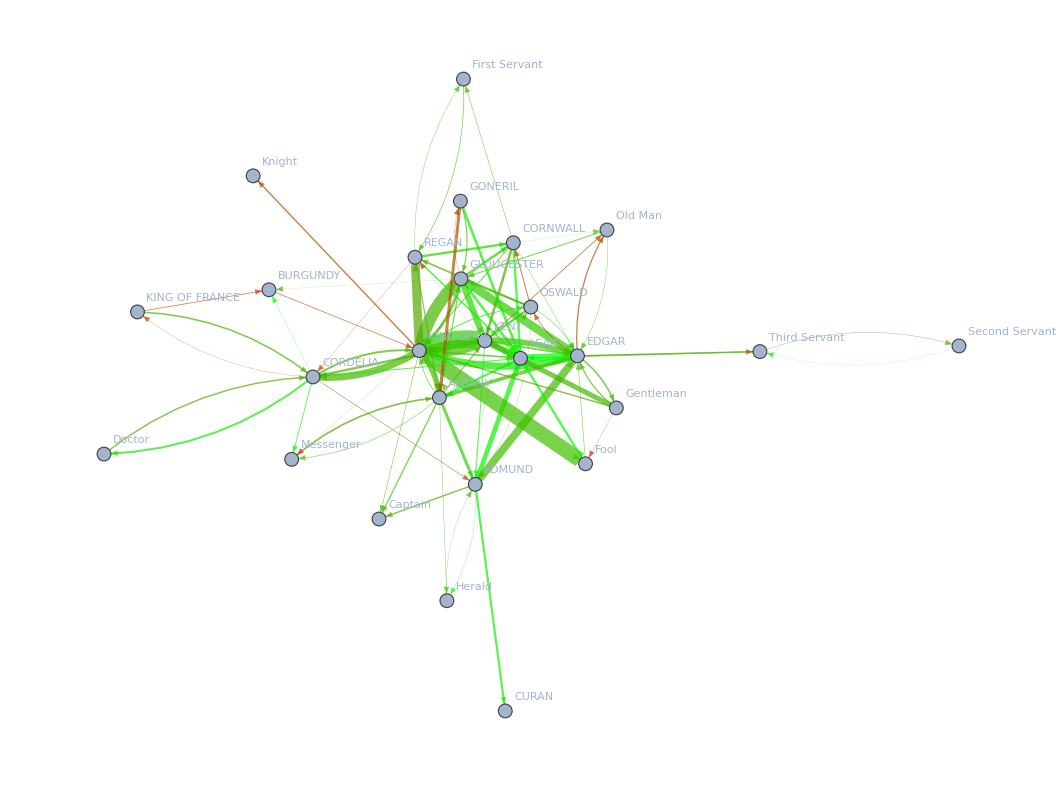

-Graphics-

```mathematica
edgeThickness=Thread[viableRules->(Thickness[#]&/@viableThickness)];
edgeFormat=Table[viableRules⟦i⟧->Directive[Values[edgeThickness]⟦i⟧,Values[edgeColors]⟦i⟧],{i,1,Length[edgeColors]}];
g=Graph[viableRules,VertexLabels->All,EdgeStyle->edgeFormat]
CommunityGraphPlot[g]
```